```mathematica
(*Quit[]*)
```

# B_c(p1)→χ_cJ(p2, {α,β}) + W_μ(q)

All form factors

## Init

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/luchinsky/Dropbox/DskD/Work/bc/bc_chi_npi/Math

```mathematica
<<MyPackages`HistV2`
```

```mathematica
chiList = {"chi_c0", "chi_c1", "chi_c2"};
```

```mathematica
<<"./mdat/amps.mdat";
```

```mathematica
<<"./mdat/ebert_ff.mdat";
```

## Intro

```mathematica
gammaTot = (6.6*10^-22 10^-3)/(0.5*10^-12);
```

```mathematica
Clear[getMcc];
(* 1P masses from PDG *)
GeV=1.; MeV=10^-3 GeV;
$MBc = 6274.47MeV;
$Vbc = 40.8*10^-3;
$mPi = 0.140GeV;
$a1 = 1.14;
getMcc[out_]:=Switch[out,"chi_c0", 3414.71MeV,"chi_c1", 3510.67MeV,"chi_c2", 3556.17MeV]
```

```mathematica
Clear[Ngamma];
Ngamma[out_, outL_, fffit_]:=Module[{
$Mcc=getMcc[out],
$q2=Switch[outL,"P", mPi, "V", mV, "W",q2]
},
gamma[out, outL]//.{
beta -> √(1-((Mcc+√q2)/MBc)^2)√(1-((Mcc-√q2)/MBc)^2),
GF->1.16*10^-5 GeV^-2,fP->130MeV,fV->208MeV,
Vuq ->0.973,Vbc-> 40.8*10^-3,a1 ->$a1
}//.{MBc -> $MBc, mPi->$mPi, mV->775MeV, Mcc->$Mcc, q2->$q2}/.fffit]
Ngamma[out_, "enu", fffit_]:=Ngamma[out,"W", fffit]/.{rhoL[_]->0, rhoT[_]->1/(6 π^2)}
```

```mathematica
Clear[q2Max];
q2Max[out_]:=($MBc-getMcc[out])^2;
```

```mathematica
Clear[BR];
BR::usage="BR[out, outL, ffName] -- my prediction for the branching fraction Bc -> out + outL using FF set ffName (in %)";
Clear[$BR];
$BR::usage="BR[out, outL, ffName] -- prediction for the branching fraction Bc -> out + outL using FF set ffName, presented in the paper (in %)";
```

## Ebert

```mathematica
ffName = "Ebert";
```

```mathematica
<<"./mdat/ebert_ff.mdat";
FFRule = ffFitRule
```

{fPlus(q2_):>0.000233941 q2^3+0.000443859 q2^2+0.0269818 q2+0.273511,fMinus(q2_):>-0.00159414 q2^3+0.00281221 q2^2-0.100528 q2-0.788861,hV1(q2_):>0.000431254 q2^3-0.00165985 q2^2+0.00638611 q2-0.0724952,hV2(q2_):>-0.00208917 q2^3+0.00655251 q2^2-0.0815061 q2-0.427086,hV3(q2_):>0.00334759 q2^3-0.0101288 q2^2+0.147855 q2+0.972119,hA(q2_):>-0.00164792 q2^3+0.000324688 q2^2-0.1251 q2-1.08075,tV(q2_):>-0.00374044 q2^3+0.0154285 q2^2-0.143736 q2-0.759328,tA1(q2_):>-0.000757811 q2^3+0.000382859 q2^2-0.0582915 q2-0.584589,tA2(q2_):>-0.00195244 q2^3+0.0137398 q2^2-0.0298194 q2+0.0939175,tA3(q2_):>0.0000646081 q2^3-0.000829955 q2^2+0.00338526 q2-0.00203697}

### Two-Body Decays

```mathematica
Clear[$gamma];
$gamma::usage="$gamma[out, outL, type] is the width of Bc -> out outL decay from tables II, VI (in 10^-15GeV)";
$gamma[out_,outL_]:=$gamma[out,outL,"1P"];
(* Table VI *)
$gamma["chi_c0","P"] = 0.23($a1)^2;
$gamma["chi_c0","V"] = 0.64($a1)^2;
$gamma["chi_c1","P"] = 0.22($a1)^2;
$gamma["chi_c1","V"] = 0.16($a1)^2;
$gamma["chi_c2","P"] = 0.41($a1)^2;
$gamma["chi_c2","V"] = 1.18($a1)^2;
```

```mathematica
$BR["chi_c0", "enu", ffName]=0.087;
$BR["chi_c1", "enu", ffName]=0.082;
$BR["chi_c2", "enu", ffName]=0.16;
$BR["chi_c0", "P", ffName]=0.021; $BR["chi_c0", "V", ffName]=0.058;
$BR["chi_c1", "P", ffName]=0.020; $BR["chi_c1", "V", ffName]=0.015;
$BR["chi_c2", "P", ffName]=0.038; $BR["chi_c2", "V", ffName]=0.11;
```

```mathematica
outL="P";
Do[
BR[out, outL, ffName]=10^2 Ngamma[out, outL, FFRule]/gammaTot;
Print["Bc ->"<> out" "<>outL<>":\t this/Ebert=", 10^15 Ngamma[out, outL, ffFitRule]/$gamma[out,outL], "\t Br this/Ebert=", BR[out, outL,ffName]/$BR[out, outL, ffName]]
,{out, chiList}]
```

Bc ->chi_c0  P:	 this/Ebert=0.987324	 Br this/Ebert=1.06464

Bc ->chi_c1  P:	 this/Ebert=0.0582581	 Br this/Ebert=0.0630935

Bc ->chi_c2  P:	 this/Ebert=0.958299	 Br this/Ebert=1.01797

```mathematica
outL="V";
Do[
BR[out, outL, ffName]=10^2 Ngamma[out, outL, FFRule]/gammaTot;
Print["Bc ->"<> out" "<>outL<>":\t this/Ebert=", 10^15 Ngamma[out, outL, ffFitRule]/$gamma[out,outL], "\t Br this/Ebert=", BR[out, outL,ffName]/$BR[out, outL, ffName]]
,{out, chiList}]
```

Bc ->chi_c0  V:	 this/Ebert=0.703591	 Br this/Ebert=0.764378

Bc ->chi_c1  V:	 this/Ebert=0.865832	 Br this/Ebert=0.909281

Bc ->chi_c2  V:	 this/Ebert=0.694878	 Br this/Ebert=0.733895

### Semileptonic decays

```mathematica
Clear[extractFF];
extractFF::usage="extractFF[json, num]";
extractFF[json_, n_, fact_:1]:=Module[{name, data},
name = json⟦3,2,n,1,2⟧;
data = json⟦3,2,n,5,2,All,3,2⟧;
data⟦All,2⟧=fact*data⟦All,2⟧;
Return[<|"name"->name,"data"->data|>]
]
```

```mathematica
Clear[getFileNameName];
Options[getFileName]={Var->"m2_0m1"};
getFileName[out_, mode_, ff_, OptionsPattern[]]:="../c++/results/B_c+_"<>out<>"_"<>mode<>"_ff"<>ff<>"/"<>OptionValue[Var]<>".txt";
getFileName[out_, mode_, opt:OptionsPattern[]]:=getFileName[out, mode, "1", opt];
```

```mathematica
Clear[readROOT];
Options[readROOT]={Norm->False, Color->Red};
readROOT[fileName_,OptionsPattern[]]:=Module[{root},
root = ReadList[fileName,{Number,Number,Number}];
If[Head[root]=!=List,
Print["File not found",  fileName];
Abort[];
];
root = HST2D[{#⟦1⟧,#⟦2⟧±#⟦3⟧}&/@root, PlotStyle->OptionValue[Color]];
If[OptionValue[Norm]=!=False,
root *= OptionValue[Norm]/IntegralHST[root];
];
root
]
```

```mathematica
Clear[NormalizeHST];
Options[NormalizeHST]={Norm->1};
NormalizeHST[hist_, OptionsPattern[]]:=OptionValue[Norm]*hist/IntegralHST[hist];
```

```mathematica
Clear[distEE];
distEE::usage="distEE[out, ffName]";
Do[
distEE[out, ffName] = extractFF[Import["../literatute/Ebert_FFs/fig4_"<>StringReplace[out,"_"->""]<>"_1P.json"], 1]["data"];
distEE[out, ffName] = 100*10^-13($Vbc)^2 HST2D[distEE[out,ffName]]/gammaTot;
,{out, chiList}];
```

```mathematica
Clear[genENuPlot];
genENuPlot::usage = "genENuPlot[out]";
genENuPlot[out_]:=Module[{},
BR[out, "enu", ffName]=100NIntegrate[Ngamma[out,"enu", ffFitRule],{q2,0,q2Max[out]}]/gammaTot;
Print["Br[this]/Br[Ebert]=",BR[out, "enu", ffName]/$BR[out, "enu", ffName]];
root=readROOT[getFileName[out, "enu", "1"], Norm-> $BR[out, "enu", ffName]];
Show[
PlotHST@NormalizeHST@distEE[out, ffName],
Plot[100*Ngamma[out,"enu", ffFitRule]/gammaTot/BR[out, "enu", ffName], {q2, 0.2,q2Max[out]}],
PlotHST@NormalizeHST@root,
AxesLabel->{"q2, GeV^2", "1/Γ ⅆΓ/ⅆq^2, 1/GeV^2"}, PlotLabel->out, PlotRange->All]
]
```

Br[this]/Br[Ebert]=1.36564

Br[this]/Br[Ebert]=1.30819

Br[this]/Br[Ebert]=1.29717

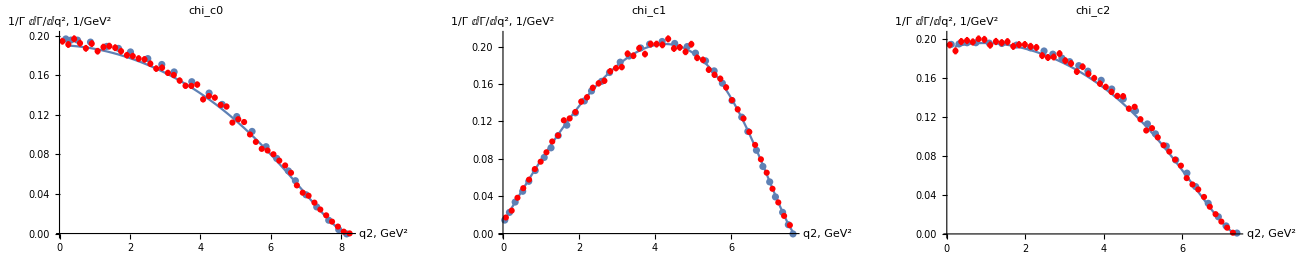

```mathematica
GraphicsGrid[{Table[genENuPlot[out], {out, chiList}]}, ImageSize->1300]
```

### nπ decays

```mathematica
<<"./mdat/rhoT.mdat";
```

```mathematica
Clear[genNPiPlot];
genNPiPlot::usage="genNPiPlot[out, mPi]";
genNPiPlot[out_, nPi_, ffName_]:=Module[{},
mode = ToString[nPi]<>"pi";react= "Bc→"<>out<>" "<>mode;
BR[out, mode,ffName]= NIntegrate[100/gammaTot Ngamma[out,"W", FFRule]/.{rhoL[_]->0,rhoT[_]->ConstNπ[nPi]*FqNπ[nPi]},{q2, (nPi*$mPi)^2,q2Max[out]}];
Print["Br[",react,"]:=", BR[out, mode,ffName],"%"];
ffNum=Switch[ffName,"Ebert","1","Wang","2"];
root = readROOT[getFileName[out,mode,ffNum],Norm->BR[out, mode,ffName]];
Show[
PlotHST[1.1root],
Plot[100/gammaTot Ngamma[out,"W", FFRule]/.{rhoL[_]->0,rhoT[_]->ConstNπ[nPi]*FqNπ[nPi]},{q2, (nPi*$mPi)^2,q2Max[out]}, PlotRange->All]
,PlotRange->All, PlotLabel->react]
]
```

Br[Bc→chi_c0 2pi]:=0.0597652%

Br[Bc→chi_c1 2pi]:=0.0185221%

Br[Bc→chi_c2 2pi]:=0.108223%

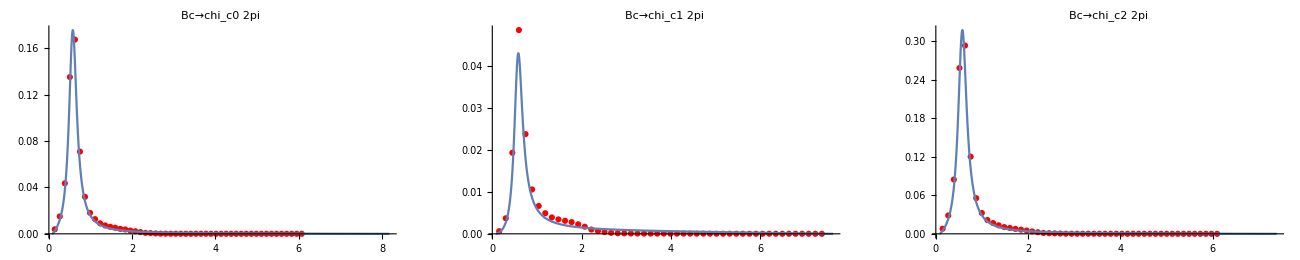

```mathematica
GraphicsGrid[{Table[genNPiPlot[out, 2, ffName],{out,chiList}]}, ImageSize->1300]
```

Br[Bc→chi_c0 3pi]:=0.0371442%

Br[Bc→chi_c1 3pi]:=0.0229855%

Br[Bc→chi_c2 3pi]:=0.068821%

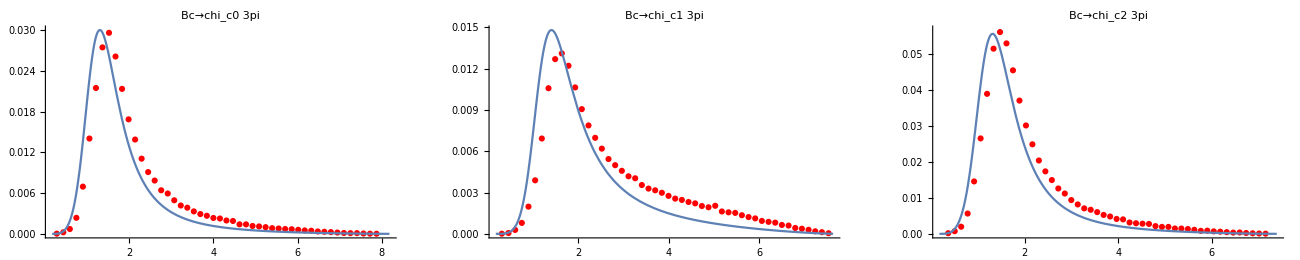

```mathematica
GraphicsGrid[{Table[genNPiPlot[out, 3, ffName],{out,chiList}]}, ImageSize->1300]
```

Br[Bc→chi_c0 5pi]:=0.00378203%

Br[Bc→chi_c1 5pi]:=0.00462799%

Br[Bc→chi_c2 5pi]:=0.00656311%

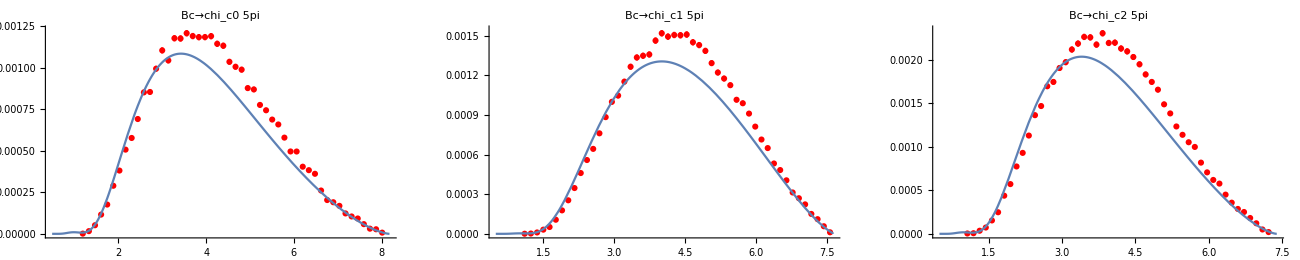

```mathematica
GraphicsGrid[{Table[genNPiPlot[out, 5, ffName],{out,chiList}]}, ImageSize->1300]
```

## Wang

```mathematica
ffName = "Wang";
```

```mathematica
<<"./mdat/wang_ff.mdat";
FFRule = ffFitRule$Wang
```

{fPlus(q2_):>-0.000465616 q2^3+0.002523 q2^2-0.0400244 q2-0.339914,fMinus(q2_):>0.00108867 q2^3-0.00879204 q2^2+0.088168 q2+0.77019,hV1(q2_):>0.000221592 q2^3-0.000913403 q2^2+0.0103316 q2-0.244354,hV2(q2_):>-0.000565963 q2^3+0.00426655 q2^2-0.0602775 q2-0.710388,hV3(q2_):>0.00071155 q2^3-0.00685796 q2^2+0.0899868 q2+1.49342,hA(q2_):>0.000614869 q2^3-0.00513732 q2^2+0.090039 q2+1.27202,tV(q2_):>0.000591919 q2^3-0.00523579 q2^2+0.101539 q2+2.01927,tA1(q2_):>-0.000688005 q2^3+0.00543166 q2^2-0.068395 q2-0.988895,tA2(q2_):>-0.00121872 q2^3+0.00992445 q2^2-0.0475703 q2-0.292165,tA3(q2_):>0.000339803 q2^3-0.00108563 q2^2+0.101109 q2+1.34214}

### Two-Body Decays

```mathematica
$BR["chi_c0", "enu", ffName]=0.13±0.03;
$BR["chi_c1", "enu", ffName]=0.11±0.03;
$BR["chi_c2", "enu", ffName]=0.10±0.03;
$BR["chi_c0", "P", ffName]=0.031±0.004; $BR["chi_c0", "V", ffName]=0.076±0.009;
$BR["chi_c1", "P", ffName]=0.0021±0.0002; $BR["chi_c1", "V", ffName]=0.023±0.002;
$BR["chi_c2", "P", ffName]=0.021±0.005; $BR["chi_c2", "V", ffName]=0.056±0.011;
```

```mathematica
outL="P";
Do[
BR[out, outL, ffName]=10^2 Ngamma[out, outL, FFRule]/gammaTot;
Print["Bc ->"<> out" "<>outL<> "\t Br this/Ebert=", BR[out, outL,ffName]/$BR[out, outL, ffName]]
,{out, chiList}]
```

Bc ->chi_c0  P	 Br this/Ebert=1.12665±0.145375

Bc ->chi_c1  P	 Br this/Ebert=1.31132±0.124887

Bc ->chi_c2  P	 Br this/Ebert=3.33061±0.793003

```mathematica
outL="V";
Do[
BR[out, outL, ffName]=10^2 Ngamma[out, outL, FFRule]/gammaTot;
Print["Bc ->"<> out" "<>outL<> "\t Br this/Ebert=", BR[out, outL,ffName]/$BR[out, outL, ffName]]
,{out, chiList}]
```

Bc ->chi_c0  V	 Br this/Ebert=0.917103±0.108604

Bc ->chi_c1  V	 Br this/Ebert=1.08337±0.0942061

Bc ->chi_c2  V	 Br this/Ebert=2.75357±0.540881

### Semileptonic decays

```mathematica
Clear[extractNames];
extractNames[json_]:=Module[{names = json⟦3,2,All,1,2⟧}, Table[{i,names⟦i⟧},{i,Length[names]}]];
```

```mathematica
json = Import["../literatute/1107.0474/Fig5_e.json"];
names = extractNames[json]
```

(1 | chi_c0
2 | chi_c1
3 | chi_c2)

```mathematica
Clear[genEnuPlot]
genEnuPlot::usage="genEnuPlot[out]";
genENuPlot[out_]:=Module[{},
BR[out, "enu",ffName] = NIntegrate[100/gammaTot Ngamma[out,"enu", FFRule],{q2, 0, q2Max[out]}] ;
root = readROOT[getFileName[out,"enu","2",Var->"m2_0m1"], Norm->1];
PlotQ2 = Show[
Plot[100/gammaTot Ngamma[out,"enu", FFRule]/BR[out, "enu",ffName], {q2, 0.2,q2Max[out]}],
PlotHST[root]
, AxesLabel->{"q2, GeV^2", "~ⅆΓ/dq2"}, PlotLabel->"Bc -> "<>out<>"e nu"];
pap =NormalizeHST@HST2D[extractFF[json, Select[names, #⟦2⟧==out&][[1,1]]]["data"]];
root = readROOT[getFileName[out,"enu","2",Var->"e_2"], Norm->1];
PlotEE = Show[
PlotHST[pap, Joined->True], PlotHST[root]
,AxesLabel->{"Ee, GeV", "1/Γ ⅆΓ/ⅆEe"}, PlotLabel->"Bc -> "<>out<>"e nu"];
Print["Br[Bc->"<>out<>"+enu]=",BR[out, "enu",ffName],"\t this/Wang=",BR[out, "enu",ffName]/$BR[out, "enu",ffName]];
GraphicsGrid[{{PlotQ2, PlotEE}}, ImageSize->1000]
];
```

Br[Bc->chi_c0+enu]=0.178709	 this/Wang=1.37468±0.317234

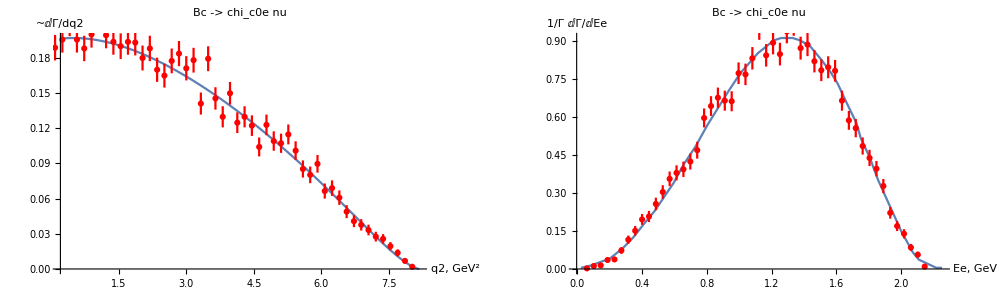

```mathematica
genENuPlot["chi_c0"]
```

Br[Bc->chi_c1+enu]=0.149007	 this/Wang=1.35461±0.369438

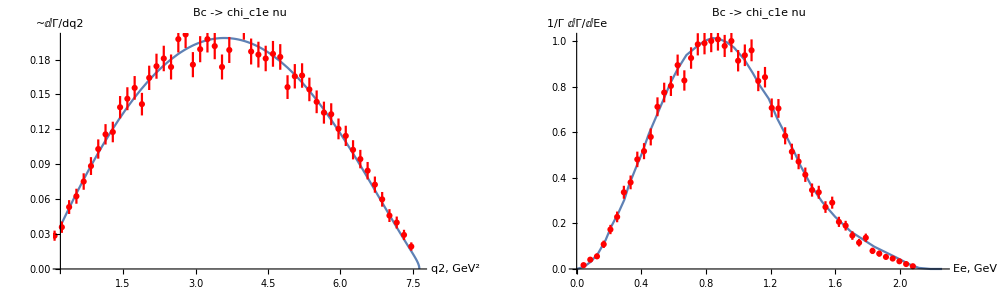

```mathematica
genENuPlot["chi_c1"]
```

Br[Bc->chi_c2+enu]=0.378609	 this/Wang=3.78609±1.13583

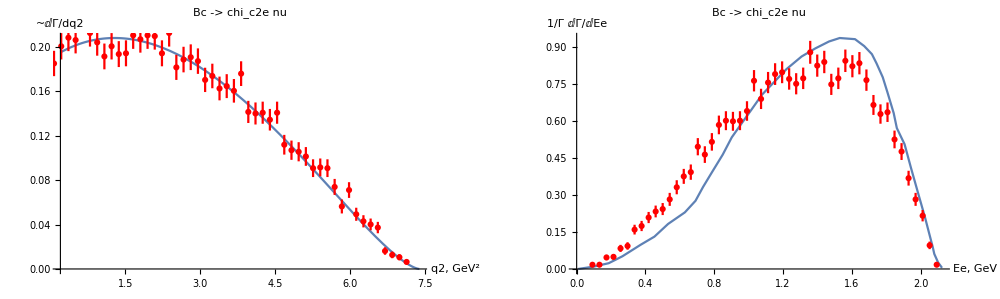

```mathematica
genENuPlot["chi_c2"]
```

### nπ decays

Br[Bc→chi_c0 2pi]:=0.0935564%

Br[Bc→chi_c1 2pi]:=0.0327829%

Br[Bc→chi_c2 2pi]:=0.205098%

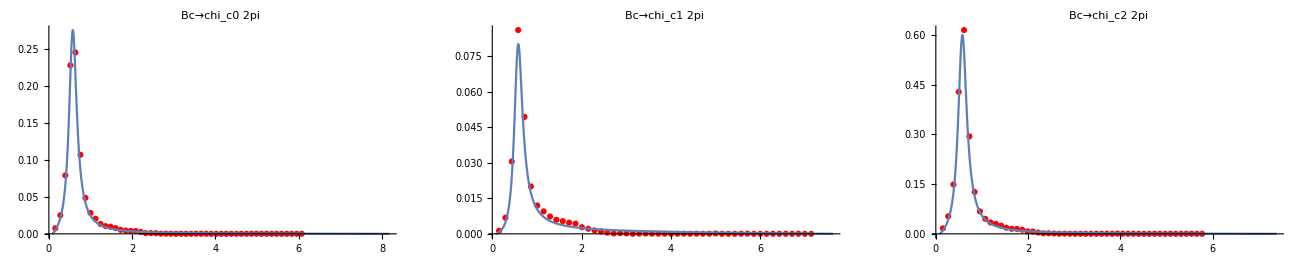

```mathematica
GraphicsGrid[{Table[genNPiPlot[out, 2, ffName],{out,chiList}]}, ImageSize->1300]
```

Br[Bc→chi_c0 3pi]:=0.0578708%

Br[Bc→chi_c1 3pi]:=0.0372543%

Br[Bc→chi_c2 3pi]:=0.132353%

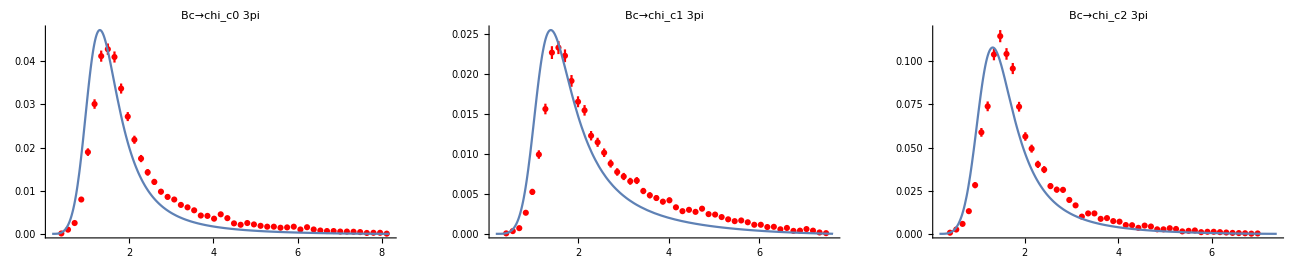

```mathematica
GraphicsGrid[{Table[genNPiPlot[out, 3, ffName],{out,chiList}]}, ImageSize->1300]
```

Br[Bc→chi_c0 5pi]:=0.00555705%

Br[Bc→chi_c1 5pi]:=0.00613793%

Br[Bc→chi_c2 5pi]:=0.0116217%

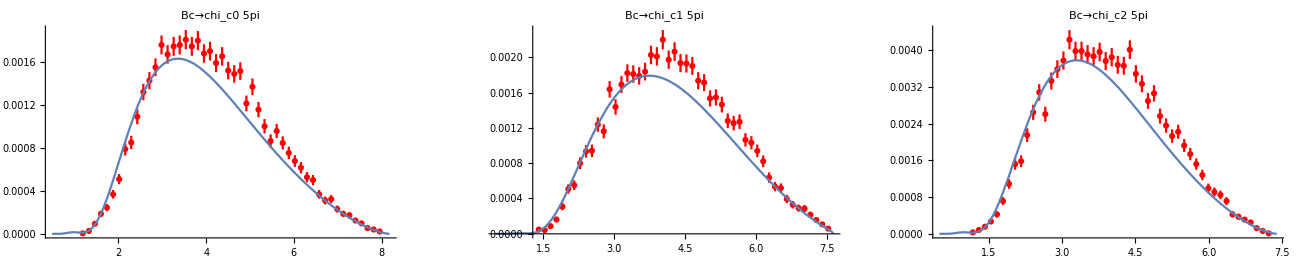

```mathematica
GraphicsGrid[{Table[genNPiPlot[out, 5, ffName],{out,chiList}]}, ImageSize->1300]
```

## Combined Tables

```mathematica
tab = Table[
Flatten[Table[BR[out,outL, ffName],{out, chiList},{ffName,{"Ebert","Wang"}}]]
,{outL,{"enu","P","V","2pi", "3pi", "5pi"}}];
tab = Round[tab,0.001];
colNames = Flatten[Table[out<>" ["<>ffName<>"]",{out, chiList},{ffName,{"Ebert","Wang"}}]];
Print["Predictions Table\n",
Grid[
MapThread[Prepend, {Prepend[tab, colNames],{" ","enu","P","V","2pi", "3pi", "5pi"}}]
,Dividers->{{2->True, 4->True, 6->True}, {2->True}}, Alignment->Right]
]
```

Predictions Table
  | chi_c0 [Ebert] | chi_c0 [Wang] | chi_c1 [Ebert] | chi_c1 [Wang] | chi_c2 [Ebert] | chi_c2 [Wang]
enu | 0.119 | 0.179 | 0.107 | 0.149 | 0.208 | 0.379
P | 0.022 | 0.035 | 0.001 | 0.003 | 0.039 | 0.07
V | 0.044 | 0.07 | 0.014 | 0.025 | 0.081 | 0.154
2pi | 0.06 | 0.094 | 0.019 | 0.033 | 0.108 | 0.205
3pi | 0.037 | 0.058 | 0.023 | 0.037 | 0.069 | 0.132
5pi | 0.004 | 0.006 | 0.005 | 0.006 | 0.007 | 0.012

```mathematica
tab = Table[
Flatten[Table[$BR[out,outL, ffName],{out, chiList},{ffName,{"Ebert","Wang"}}]]
,{outL,{"enu","P","V"}}];
colNames = Flatten[Table[out<>" ["<>ffName<>"]",{out, chiList},{ffName,{"Ebert","Wang"}}]];
Print["Papers' table\n",
Grid[
MapThread[Prepend, {Prepend[tab, colNames],{" ","enu","P","V"}}]
,Dividers->{None, {2->True}}, Alignment->Right]
]
```

Papers' table
  | chi_c0 [Ebert] | chi_c0 [Wang] | chi_c1 [Ebert] | chi_c1 [Wang] | chi_c2 [Ebert] | chi_c2 [Wang]
enu | 0.087 | 0.13±0.03 | 0.082 | 0.11±0.03 | 0.16 | 0.1±0.03
P | 0.021 | 0.031±0.004 | 0.02 | 0.0021±0.0002 | 0.038 | 0.021±0.005
V | 0.058 | 0.076±0.009 | 0.015 | 0.023±0.002 | 0.11 | 0.056±0.011

```mathematica
ffName="Ebert";
tab = Table[
Flatten[Table[{BR[out,outL, ffName], $BR[out, outL, ffName],BR[out,outL, ffName]/$BR[out, outL, ffName]},{out, chiList}]]
,{outL,{"enu","P","V"}}];
tab = Round[tab,0.001];
colNames = Flatten[Table[{"this","work","this/work"},{out, chiList}]];
Print["Comparison:",ffName,"\n",
Grid[
MapThread[Prepend, {Prepend[tab, colNames],{" ","enu","P","V"}}]
,Dividers->{{5->True,8->True}, {2->True}}, Alignment->Right]
]
```

Comparison:Ebert
  | this | work | this/work | this | work | this/work | this | work | this/work
enu | 0.119 | 0.087 | 1.366 | 0.107 | 0.082 | 1.308 | 0.208 | 0.16 | 1.297
P | 0.022 | 0.021 | 1.065 | 0.001 | 0.02 | 0.063 | 0.039 | 0.038 | 1.018
V | 0.044 | 0.058 | 0.764 | 0.014 | 0.015 | 0.909 | 0.081 | 0.11 | 0.734

```mathematica
Clear[RemoveError];
RemoveError[a_]:=a;
RemoveError[a_±b_]:=a
```

```mathematica
ffName="Wang";
tab = Table[
Flatten[Table[{BR[out,outL, ffName], RemoveError[$BR[out, outL, ffName]],RemoveError[BR[out,outL, ffName]/$BR[out, outL, ffName]]},{out, chiList}]]
,{outL,{"enu","P","V"}}];
(*tab = Round[tab,0.001];*)
colNames = Flatten[Table[{"this","work","this/work"},{out, chiList}]];
Print["Comparison:",ffName,"\n",
Grid[
MapThread[Prepend, {Prepend[tab, colNames],{" ","enu","P","V"}}]
,Dividers->{{5->True,8->True}, {2->True}}, Alignment->Right]
]
```

Comparison:Wang
  | this | work | this/work | this | work | this/work | this | work | this/work
enu | 0.178709 | 0.13 | 1.37468 | 0.149007 | 0.11 | 1.35461 | 0.378609 | 0.1 | 3.78609
P | 0.0349263 | 0.031 | 1.12665 | 0.00275377 | 0.0021 | 1.31132 | 0.0699428 | 0.021 | 3.33061
V | 0.0696998 | 0.076 | 0.917103 | 0.0249175 | 0.023 | 1.08337 | 0.1542 | 0.056 | 2.75357